#### build/load

```mathematica
BuildCompilerLibraries["D:\\github\\prototypes\\Prototypes\\Source\\Compiler"]
```

D:\github\prototypes\Prototypes\Source\Compiler\Source\Collatz.wl

D:\github\prototypes\Prototypes\Source\Compiler\Source\FibonacciNumber.wl

D:\github\prototypes\Prototypes\Source\Compiler\Source\Integer64Identity.wl

D:\github\prototypes\Prototypes\Source\Compiler\Source\Mandelbrot.wl

```mathematica
LoadCompilerLibraries["D:\\github\\prototypes\\Prototypes\\Source\\Compiler"]
```

D:\github\prototypes\Prototypes\Source\Compiler\Libraries\Windows-x86-64\Collatz.dll

D:\github\prototypes\Prototypes\Source\Compiler\Libraries\Windows-x86-64\FibonacciNumber.dll

D:\github\prototypes\Prototypes\Source\Compiler\Libraries\Windows-x86-64\Integer64Identity.dll

D:\github\prototypes\Prototypes\Source\Compiler\Libraries\Windows-x86-64\Mandelbrot.dll

#### examples

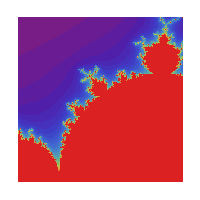

```mathematica
Mandelbrot[Table[i+I*j,{j,-1,0,0.005},{i,-1,0,0.005}]]//ArrayPlot[#,ColorFunction->"Rainbow",Frame->False,PlotRangePadding->None,ImageSize->{201,201}]&
```

```mathematica
Collatz[43]//AbsoluteTiming
```

{0.0000352,{43,130,65,196,98,49,148,74,37,112,56,28,14,7,22,11,34,17,52,26,13,40,20,10,5,16,8,4,2,1}}

```mathematica
On[CompiledCodeFunction::uncomp]
```

On::none: Message CompiledCodeFunction::uncomp not found.

```mathematica
FibonacciNumber[92]//AbsoluteTiming
```

{0.0031407,7540113804746346429}

```mathematica
FibonacciNumber[92]
```

7540113804746346429

```mathematica
Fibonacci[92]//AbsoluteTiming
```

{0.0000155,7540113804746346429}

#### experiments

```mathematica
ClearAll[f1,f2,f3,f]
```

```mathematica
f1=FunctionCompile[Function[{Typed[x,"Integer64"]},x]];
```

```mathematica
f2=FunctionCompile[Function[{Typed[x,"Real64"]},x]];
```

```mathematica
f3=FunctionCompile[Function[{Typed[x,"ComplexReal64"]},x]];
```

```mathematica
f[x:_Integer|_Real|_Complex]:=Switch[x,_Integer,f1,_Real,f2,_Complex,f3][x]
```

```mathematica
f[23]
```

23

```mathematica
f[3.4]
```

3.4

```mathematica
f[1+I]
```

CompiledCodeFunction::argtype: Argument type at position 1 does not match function signature.

Failure[…]

```mathematica
f[1.+I]
```

1.+1. ⅈ

```mathematica
FibonacciNumber[92]//AbsoluteTiming
```

{0.0026519,7540113804746346429}

```mathematica
FunctionCompile[Function[{Typed[n,"Integer64"]},
With[{fib=Typed[KernelFunction[FibonacciNumber],{"Integer64"}->"Integer64"]},
If[n>2,If[Mod[n,2]===0,fib[Quotient[n,2]]*(2*fib[Quotient[n,2]+1]-fib[Quotient[n,2]]),fib[Quotient[n-1,2]+1]^2+fib[Quotient[n-1,2]]^2],1]]]]
```

CompiledCodeFunction[…]

```mathematica
Quit
```

```mathematica
ClearAll[FibonacciNumber]
```

```mathematica
FibonacciNumber=FunctionCompile@Function[{Typed[n,"Integer64"]},With[{fib=Typed[KernelFunction[FibonacciNumber],{"Integer64"}->"Integer64"]},If[n>2,If[Mod[n,2]===0,fib[Quotient[n,2]]*(2*fib[Quotient[n,2]+1]-fib[Quotient[n,2]]),fib[Quotient[n-1,2]+1]^2+fib[Quotient[n-1,2]]^2],1]]]
```

CompiledCodeFunction[…]

```mathematica
FibonacciNumber[30]
```

832040